```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
G11[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo-zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G22[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo+zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G12[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p (Jtwo+Jone Cos[k]+(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
Nulls[Jtwo_,z_]:=1-G11[1,0.2,Jtwo,-0.1,z]-G22[1,0.2,Jtwo,-0.1,z]-G12[1,0.2,Jtwo,-0.1,z]^2+G11[1,0.2,Jtwo,-0.1,z]G22[1,0.2,Jtwo,-0.1,z]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[Nulls[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
a=FindRoot[Nulls[Jtwoo,z]==0,{z,z/.lst[[n,2]]}]
;
AppendTo[lst,{Jtwoo,a}];
,{n,1,199,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,200,1}];
lst
]
```

```mathematica
moduler[Lister[-1,-0.0005,0.7536715765093541]]
```

{{-0.005,0.748483},{-0.01,0.743114},{-0.015,0.737576},{-0.02,0.731879},{-0.025,0.726033},{-0.03,0.720046},{-0.035,0.713924},{-0.04,0.707673},{-0.045,0.701298},{-0.05,0.694803},{-0.055,0.68819},{-0.06,0.681461},{-0.065,0.67462},{-0.07,0.667666},{-0.075,0.660599},{-0.08,0.653421},{-0.085,0.646131},{-0.09,0.638728},{-0.095,0.63121},{-0.1,0.623576}}

```mathematica
moduler[Lister[1,0.0005,0.7536715765093541]]
```

{{0.005,0.758665},{0.01,0.763448},{0.015,0.768003},{0.02,0.772313},{0.025,0.776357},{0.03,0.780115},{0.035,0.783565},{0.04,0.786687},{0.045,0.789461},{0.05,0.79187},{0.055,0.793898},{0.06,0.795536},{0.065,0.796776},{0.07,0.797616},{0.075,0.798058},{0.08,0.798109},{0.085,0.797779},{0.09,0.797081},{0.095,0.796031},{0.1,0.794646}}

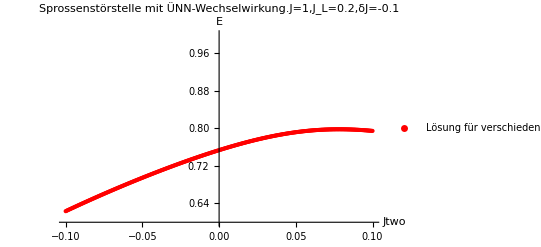

```mathematica
P = ListPlot[Fueger[moduler[Lister[-1,-0.0005,0.7536715765093541]],moduler[Lister[1,0.0005,0.7536715765093541]]],AxesLabel->{Jtwo,"E"},PlotRange->{0.6,1},PlotLegends->{"Lösung für verschiedene Jtwos"},PlotLabel->"Sprossenstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.2,δJ=-0.1",PlotStyle->Red]
```

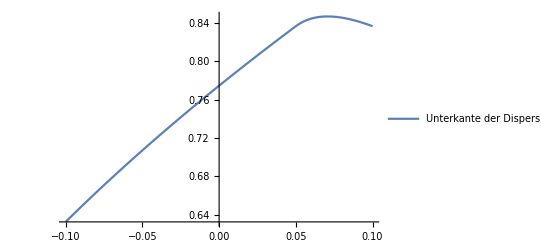

```mathematica
G = Plot[Sqrt[1+2(0.2*Cos[Inv[0.2,J]]+J*Cos[2*Inv[0.2,J]])],{J,-0.1,0.1},PlotLegends->{"Unterkante der Dispersion"}]
```

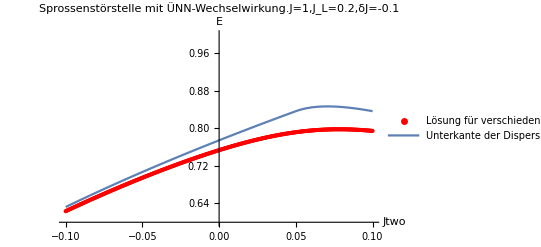

```mathematica
Show[P,G]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.0005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
differ[-1,0.2,moduler[Lister[-1,-0.005,0.7536715765093541]]]
```

{{-0.005,0.0196312},{-0.01,0.0184632},{-0.015,0.0174077},{-0.02,0.0164525},{-0.025,0.0155868},{-0.03,0.014801},{-0.035,0.0140869},{-0.04,0.0134369},{-0.045,0.0128446},{-0.05,0.012304},{-0.055,0.0118103},{-0.06,0.0113589},{-0.065,0.0109457},{-0.07,0.0105675},{-0.075,0.010221},{-0.08,0.00990348},{-0.085,0.0096126},{-0.09,0.0093462},{-0.095,0.00910237},{-0.1,0.00887942}}

```mathematica
differ[1,0.2,moduler[Lister[1,0.005,0.7536715765093541]]]
```

{{0.005,0.0223601},{0.01,0.0239531},{0.015,0.0257221},{0.02,0.027687},{0.025,0.0298688},{0.03,0.0322893},{0.035,0.0349706},{0.04,0.0379345},{0.045,0.0412016},{0.05,0.432875},{0.055,0.0476371},{0.06,0.0490547},{0.065,0.049483},{0.07,0.0492273},{0.075,0.048504},{0.08,0.0474681},{0.085,0.0462314},{0.09,0.0448744},{0.095,0.0434548},{0.1,0.0420138}}

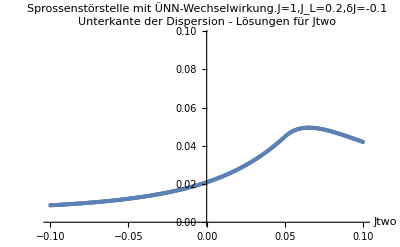

```mathematica
ListPlot[Fueger[differ[-1,0.2,moduler[Lister[-1,-0.0005,0.7536715765093541]]],differ[1,0.2,moduler[Lister[1,0.0005,0.7536715765093541]]]],AxesLabel->{Jtwo,"Unterkante der Dispersion - Lösungen für Jtwo"}, PlotLabel->"Sprossenstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.2,δJ=-0.1"]
```

```mathematica
Maxfinder[list_] := Module[{gross=0,spot=0},
Do[
If[list[[n,2]]>gross,spot=list[[n,1]]];
If[list[[n,2]]>gross,gross=list[[n,2]]];
,{n,1,400,1}];
{spot,gross}
]
```

```mathematica
Maxfinder[Fueger[moduler[Lister[-1,-0.0005,0.7536715765093541]],moduler[Lister[1,0.0005,0.7536715765093541]]]]
```

{0.078,0.798135}